# Population centroids

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Desktop/usvi-map-code

## Get centroid for country

```mathematica
cities=CityData[{All,"Brazil"}];
```

```mathematica
cities[[1]]
```

São Paulo

```mathematica
lats=Map[CityData[#,"Latitude"]&,cities];
```

```mathematica
longs=Map[CityData[#,"Longitude"]&,cities];
```

```mathematica
pops=Map[CityData[#,"Population"]&,cities];
```

```mathematica
missingPos=Union[Flatten[{Position[lats,Missing][[All,1]],Position[longs,Missing][[All,1]],Position[pops,Missing][[All,1]]}]];
```

```mathematica
lats=Delete[lats,Map[{#}&,missingPos]];
```

```mathematica
longs=Delete[longs,Map[{#}&,missingPos]];
```

```mathematica
pops=Delete[pops,Map[{#}&,missingPos]];
```

```mathematica
lats=Map[QuantityMagnitude[#]&,lats];
```

```mathematica
longs=Map[QuantityMagnitude[#]&,longs];
```

```mathematica
pops=Map[QuantityMagnitude[#]&,pops];
```

```mathematica
weights=N[pops/Total[pops]];
```

```mathematica
lats[[1]]
```

-23.53

```mathematica
weightedCentroid=Total[MapThread[{#1*#3,#2*#3}&,{lats,longs,weights}]]
```

{-18.0026,-45.6803}

```mathematica
getCentroidForCountry[country_]:=Module[{cities,lats,longs,pops,weights,missingPos},
cities=CityData[{All,country}];
lats=Map[CityData[#,"Latitude"]&,cities];
longs=Map[CityData[#,"Longitude"]&,cities];
pops=Map[CityData[#,"Population"]&,cities];
missingPos=Union[Flatten[{Position[lats,Missing][[All,1]],Position[longs,Missing][[All,1]],Position[pops,Missing][[All,1]]}]];
lats=Delete[lats,Map[{#}&,missingPos]];
longs=Delete[longs,Map[{#}&,missingPos]];
pops=Delete[pops,Map[{#}&,missingPos]];
lats=Map[QuantityMagnitude[#]&,lats];
longs=Map[QuantityMagnitude[#]&,longs];
pops=Map[QuantityMagnitude[#]&,pops];
weights=N[pops/Total[pops]];
Total[MapThread[{#1*#3,#2*#3}&,{lats,longs,weights}]]
]
```

```mathematica
getCentroidForCountry["Brazil"]
```

{-18.0026,-45.6803}

```mathematica
getCentroidForCountry["Mexico"]
```

{21.6462,-100.641}

## Countries

```mathematica
countries=Map[CanonicalName,Join[CountryData["NorthAmerica"],CountryData["SouthAmerica"]]]
```

{Anguilla,AntiguaBarbuda,Aruba,Bahamas,Barbados,Belize,Bermuda,BritishVirginIslands,Canada,CaymanIslands,CostaRica,Cuba,Curacao,Dominica,DominicanRepublic,ElSalvador,Greenland,Grenada,Guadeloupe,Guatemala,Haiti,Honduras,Jamaica,Martinique,Mexico,Montserrat,Nicaragua,Panama,PuertoRico,SaintKittsNevis,SaintLucia,SaintPierreMiquelon,SaintVincentGrenadines,SintMaarten,TrinidadTobago,TurksCaicosIslands,UnitedStates,UnitedStatesVirginIslands,Argentina,Bolivia,Brazil,Chile,Colombia,Ecuador,FalklandIslands,FrenchGuiana,Guyana,Paraguay,Peru,Suriname,Uruguay,Venezuela}

```mathematica
centroids=Map[getCentroidForCountry,countries]
```

{{18.2136,-63.0558},{17.1066,-61.8353},{12.4901,-69.9864},{25.3954,-77.5319},{13.1191,-59.6056},{17.4708,-88.4514},{32.3466,-64.71},{18.43,-64.63},{46.6795,-88.3362},{19.3101,-81.3488},{9.96464,-84.1521},{21.9455,-79.6419},{12.1194,-68.9364},{15.3843,-61.3706},{18.8507,-70.2128},{13.7123,-89.1089},{66.7336,-51.5912},{12.1441,-61.6857},{16.2631,-61.5725},{14.7709,-90.736},{18.8057,-72.4724},{14.839,-87.4764},{18.0674,-77.0575},{14.6293,-61.0108},{21.6462,-100.641},{16.7499,-62.2063},{12.3563,-86.1116},{8.85957,-80.0867},{18.3091,-66.2799},{17.3102,-54.3351},{13.9261,-60.9685},{46.8382,-56.2142},{13.1649,-61.2068},{18.0273,-63.0547},{10.4712,-61.4142},{21.6773,-71.7101},{37.671,-93.1488},{18.1952,-64.8895},{-32.8844,-61.6705},{-17.4262,-65.595},{-18.0026,-45.6803},{-33.7169,-71.1878},{5.98283,-74.8494},{-1.53179,-79.4312},{-51.7258,-57.7048},{5.01143,-52.8651},{6.54076,-58.0694},{-25.3147,-56.9082},{-10.9852,-76.5397},{5.82013,-55.2681},{-34.0967,-56.2381},{10.0747,-67.6937}}

```mathematica
circles=Map[Circle[Reverse[#],1]&,centroids];
```

```mathematica
names=MapThread[Text[#1,Reverse[#2]+{2,0},{-1,0}]&,{countries,centroids}];
```

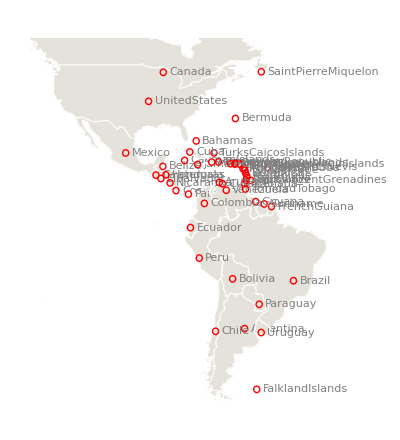

```mathematica
map=Graphics[{{EdgeForm[White],RGBColor[0.896,0.8878,0.8548],CountryData["World","SchematicPolygon"],Red,circles,Gray,names}},ImageSize->400,PlotRange->{{-130,-30},{-55,55}}]
```

## Export

```mathematica
data=MapThread[{#1,#2[[1]],#2[[2]]}&,{countries,centroids}]
```

{{Anguilla,18.2136,-63.0558},{AntiguaBarbuda,17.1066,-61.8353},{Aruba,12.4901,-69.9864},{Bahamas,25.3954,-77.5319},{Barbados,13.1191,-59.6056},{Belize,17.4708,-88.4514},{Bermuda,32.3466,-64.71},{BritishVirginIslands,18.43,-64.63},{Canada,46.6795,-88.3362},{CaymanIslands,19.3101,-81.3488},{CostaRica,9.96464,-84.1521},{Cuba,21.9455,-79.6419},{Curacao,12.1194,-68.9364},{Dominica,15.3843,-61.3706},{DominicanRepublic,18.8507,-70.2128},{ElSalvador,13.7123,-89.1089},{Greenland,66.7336,-51.5912},{Grenada,12.1441,-61.6857},{Guadeloupe,16.2631,-61.5725},{Guatemala,14.7709,-90.736},{Haiti,18.8057,-72.4724},{Honduras,14.839,-87.4764},{Jamaica,18.0674,-77.0575},{Martinique,14.6293,-61.0108},{Mexico,21.6462,-100.641},{Montserrat,16.7499,-62.2063},{Nicaragua,12.3563,-86.1116},{Panama,8.85957,-80.0867},{PuertoRico,18.3091,-66.2799},{SaintKittsNevis,17.3102,-54.3351},{SaintLucia,13.9261,-60.9685},{SaintPierreMiquelon,46.8382,-56.2142},{SaintVincentGrenadines,13.1649,-61.2068},{SintMaarten,18.0273,-63.0547},{TrinidadTobago,10.4712,-61.4142},{TurksCaicosIslands,21.6773,-71.7101},{UnitedStates,37.671,-93.1488},{UnitedStatesVirginIslands,18.1952,-64.8895},{Argentina,-32.8844,-61.6705},{Bolivia,-17.4262,-65.595},{Brazil,-18.0026,-45.6803},{Chile,-33.7169,-71.1878},{Colombia,5.98283,-74.8494},{Ecuador,-1.53179,-79.4312},{FalklandIslands,-51.7258,-57.7048},{FrenchGuiana,5.01143,-52.8651},{Guyana,6.54076,-58.0694},{Paraguay,-25.3147,-56.9082},{Peru,-10.9852,-76.5397},{Suriname,5.82013,-55.2681},{Uruguay,-34.0967,-56.2381},{Venezuela,10.0747,-67.6937}}

```mathematica
Export["centroids.tsv",data,"Table"]
```

centroids.tsv